#### Extract the prices from Wolfram's data service

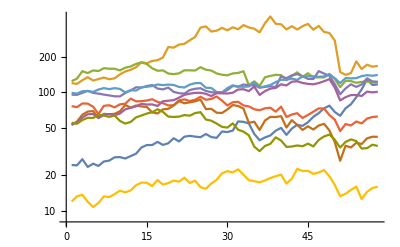

```mathematica
portfolio={"AAPL","AXP","BA","CAT","CSCO","CVX","DIS","GS","HD","IBM","INTC","JNJ","JPM","KO","MCD","MMM","MRK","MSFT","NKE","PFE","PG","TRV","UNH","UTX","V","VZ","WBA","WMT","XOM"};
figi={"BBG000B9Y5X2","BBG000BCR153","BBG000BCSV38","BBG000BF0LJ6","BBG000C3JBN9","BBG000K4NHJ5","BBG000BH4SB1","BBG000C6CH10","BBG000BKZDM1","BBG000BLNQ16","BBG000C0GFS4","BBG000BMHZY5","BBG000DMBZW1","BBG000BMX4N8","BBG000BNT1L9","BBG000BP5522","BBG000BPD257","BBG000BPHFS9","BBG000C5HTN7","BBG000BR2F10","BBG000BR2WS4","BBG000BJ82Q4","BBG000CH53T5","BBG000BW8TX8","BBG000PSL0X0","BBG000HS79Q4","BBG000BWLX00","BBG000BWXCP6","BBG000GZQBJ1"};
assetCount=Length[portfolio];
priceHistory=(QuantityMagnitude[FinancialData[#1,"Price",{{2016},{2020},"Month"}]["Path"]⟦All,2⟧]&)/@portfolio;
ListLogPlot[priceHistory,PlotRange-> All,Joined->True]
```

#### Calculate the actual returns based on the log of the difference in the asset price from month to month.

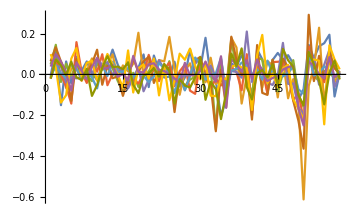

```mathematica
actualReturns=(Differences[Log[priceHistory⟦#1⟧]]&)/@Range[assetCount];
ListLinePlot[actualReturns,PlotRange->All]
```

#### The ‘Correlation’ function below is just a prepackaged way of doing this:

```mathematica
MatrixForm[Outer[((actualReturns⟦#1⟧-Mean[actualReturns⟦#1⟧]).(actualReturns⟦#2⟧-Mean[actualReturns⟦#2⟧]))/((Length[actualReturns⟦#1⟧]-1) (StandardDeviation[actualReturns⟦#1⟧] StandardDeviation[actualReturns⟦#2⟧]))&,Range[assetCount],Range[assetCount]]];
```

```mathematica
MatrixForm[Correlation[Transpose[actualReturns]]];
```

(1. | 0.198269 | 0.352865 | 0.383725 | 0.311462 | 0.370991 | 0.244959 | 0.407714 | 0.352018 | 0.315086
0.198269 | 1. | 0.36738 | 0.462294 | 0.452494 | 0.550756 | 0.28371 | 0.362732 | 0.609534 | 0.312757
0.352865 | 0.36738 | 1. | 0.390652 | 0.378524 | 0.734005 | 0.355814 | 0.34334 | 0.613741 | 0.439712
0.383725 | 0.462294 | 0.390652 | 1. | 0.480397 | 0.646578 | 0.143318 | 0.437908 | 0.545832 | 0.327819
0.311462 | 0.452494 | 0.378524 | 0.480397 | 1. | 0.536581 | 0.442603 | 0.257709 | 0.624868 | 0.302888
0.370991 | 0.550756 | 0.734005 | 0.646578 | 0.536581 | 1. | 0.42773 | 0.44746 | 0.717479 | 0.473435
0.244959 | 0.28371 | 0.355814 | 0.143318 | 0.442603 | 0.42773 | 1. | 0.149944 | 0.414802 | 0.378356
0.407714 | 0.362732 | 0.34334 | 0.437908 | 0.257709 | 0.44746 | 0.149944 | 1. | 0.378412 | 0.392181
0.352018 | 0.609534 | 0.613741 | 0.545832 | 0.624868 | 0.717479 | 0.414802 | 0.378412 | 1. | 0.283535
0.315086 | 0.312757 | 0.439712 | 0.327819 | 0.302888 | 0.473435 | 0.378356 | 0.392181 | 0.283535 | 1.)

#### Heat map to show the correlation between stock pairs.

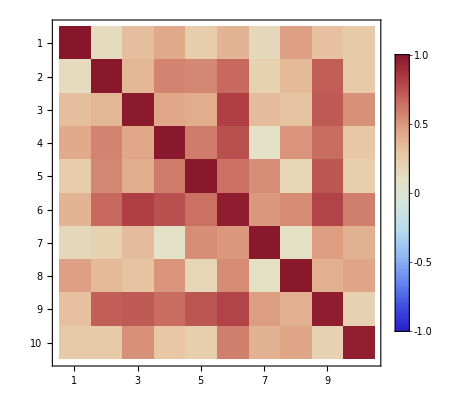

```mathematica
Legended[MatrixPlot[Correlation[Transpose[actualReturns]],ColorFunction->#],BarLegend[{#,{-1,1}}]]&@"ThermometerColors"
```

#### The variables used for the asset’s weights.

```mathematica
weights=Table[Subscript[w,i],{i,Range[assetCount]},{j,1}];
t=ConstantArray[1,assetCount];
```

#### This is the formula used to minimize the mean variance.

```mathematica
covariance=Covariance[Transpose[actualReturns]];
portfolioVariance=weightsᵀ.covariance.weights;
portfolioVariance=Expand[portfolioVariance⟦1⟧⟦1⟧];
```

{{w_7 (0.000895824 w_1+0.00143463 w_2+0.00109075 w_3+0.000464976 w_4+0.00125266 w_5+0.00207382 w_6+0.00184529 w_7+0.000602911 w_8+0.00111715 w_9+0.00122478 w_10)+w_9 (0.00187889 w_1+0.00449853 w_2+0.00274597 w_3+0.00258462 w_4+0.00258115 w_5+0.00507713 w_6+0.00111715 w_7+0.00222074 w_8+0.00393078 w_9+0.00133959 w_10)+w_5 (0.00174698 w_1+0.00350939 w_2+0.00177971 w_3+0.00239047 w_4+0.00434081 w_5+0.00399016 w_6+0.00125266 w_7+0.0015893 w_8+0.00258115 w_9+0.00150381 w_10)+w_4 (0.00246726 w_1+0.00411007 w_2+0.00210552 w_3+0.00570422 w_4+0.00239047 w_5+0.00551174 w_6+0.000464976 w_7+0.00309581 w_8+0.00258462 w_9+0.00186577 w_10)+w_1 (0.00724758 w_1+0.00198694 w_2+0.00214376 w_3+0.00246726 w_4+0.00174698 w_5+0.00356476 w_6+0.000895824 w_7+0.00324896 w_8+0.00187889 w_9+0.00202139 w_10)+w_3 (0.00214376 w_1+0.00308617 w_2+0.00509263 w_3+0.00210552 w_4+0.00177971 w_5+0.00591207 w_6+0.00109075 w_7+0.00229345 w_8+0.00274597 w_9+0.00236464 w_10)+w_8 (0.00324896 w_1+0.0039968 w_2+0.00229345 w_3+0.00309581 w_4+0.0015893 w_5+0.00472733 w_6+0.000602911 w_7+0.00876164 w_8+0.00222074 w_9+0.00276633 w_10)+w_2 (0.00198694 w_1+0.0138569 w_2+0.00308617 w_3+0.00411007 w_4+0.00350939 w_5+0.0073175 w_6+0.00143463 w_7+0.0039968 w_8+0.00449853 w_9+0.00277437 w_10)+w_6 (0.00356476 w_1+0.0073175 w_2+0.00591207 w_3+0.00551174 w_4+0.00399016 w_5+0.0127391 w_6+0.00207382 w_7+0.00472733 w_8+0.00507713 w_9+0.00402675 w_10)+(0.00202139 w_1+0.00277437 w_2+0.00236464 w_3+0.00186577 w_4+0.00150381 w_5+0.00402675 w_6+0.00122478 w_7+0.00276633 w_8+0.00133959 w_9+0.00567871 w_10) w_10}}

#### In order to chart the returns, we need to know the range of possible returns. The minimum and maximum return for a portfolio are simply the best and worst annual returns for a single asset.

```mathematica
minimumReturn=12 Min[Mean/@actualReturns];
maximumReturn=12 Max[Mean/@actualReturns];
```

#### Calculate the weights that give us the minimum mean variance and keeps the total weight at unity.

```mathematica
yearlyWeightedReturns = First[Total[12*weights*Mean /@ actualReturns]]; 
efficientFrontier = Table[{Sqrt[FindMinimum[{portfolioVariance, weightsᵀ.t == 1 && yearlyWeightedReturns == i}, weights][[1]]], i}, {i, minimumReturn, maximumReturn, 0.02}];
```

#### Let' s see how changing the desired return effects the risk.

```mathematica
Manipulate[
minimum=FindMinimum[{portfolioVariance,weightsᵀ.t == 1&&yearlyWeightedReturns==return},weights];
plot1=BarChart[{Last[minimum][[#,2]]&/@Range[assetCount]},
PlotRange->{-0.4,0.6},
AxesOrigin->{0,-0.4},
ImageSize->Large,
ChartLabels->portfolio];
minimumVariance=First[minimum];
plot2=ListLinePlot[
efficientFrontier,
Epilog->{Red,PointSize->Large,Point[{Sqrt[ First[minimum]],return}]},
Frame->True,
FrameLabel->{"σ","Expected portfolio return"},
PlotRange->{{0,Automatic},Automatic},
BaseStyle->16,
ImageSize->Large];
GraphicsGrid[{{plot1},{plot2}}],
{{return,0.1,"Desired Return"},minimumReturn,maximumReturn,Appearance->"Labeled"}]
```

Part::partw: Part 2 of {w_1} does not exist.

Part::partw: Part 2 of {w_2} does not exist.

Part::partw: Part 2 of {w_3} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListLinePlot::lpn: efficientFrontier is not a list of numbers or pairs of numbers.

```mathematica
portfolio={"AAPL","AXP","BA","CAT","CSCO","CVX","DIS","GS","HD","IBM","INTC","JNJ","JPM","KO","MCD","MMM","MRK","MSFT","NKE","PFE","PG","TRV","UNH","UTX","V","VZ","WBA","WMT","XOM"};
figi={"BBG000B9Y5X2","BBG000BCR153","BBG000BCSV38","BBG000BF0LJ6","BBG000C3JBN9","BBG000K4NHJ5","BBG000BH4SB1","BBG000C6CH10","BBG000BKZDM1","BBG000BLNQ16","BBG000C0GFS4","BBG000BMHZY5","BBG000DMBZW1","BBG000BMX4N8","BBG000BNT1L9","BBG000BP5522","BBG000BPD257","BBG000BPHFS9","BBG000C5HTN7","BBG000BR2F10","BBG000BR2WS4","BBG000BJ82Q4","BBG000CH53T5","BBG000BW8TX8","BBG000PSL0X0","BBG000HS79Q4","BBG000BWLX00","BBG000BWXCP6","BBG000GZQBJ1"};
```